```mathematica
matrix=Table[RandomInteger[],50];
```

```mathematica
countdata=Table[0,50];
```

```mathematica
immunitycoefficient=0.01;
```

```mathematica
spreadcoefficient=2;
```

```mathematica
sicknessperiod=13;
```

```mathematica
deathprobability=1/2;
```

```mathematica
clist={};
```

```mathematica
immunity=Table[RandomChoice[{immunitycoefficient,1-immunitycoefficient}->{True,False}],Length[matrix]];
```

## Loop

```mathematica
{Table[{countdata=countdata+matrix;
neighbors=Table[Table[Flatten[{matrix,matrix,matrix},1][[Length[matrix]+r+n]],{n,Flatten[{Table[-1*g,{g,spreadcoefficient}],Table[1*g,{g,spreadcoefficient}]}]}],{r,Length[matrix]}];
matrix=Table[If[immunity[[cell]]==False,RandomChoice[{Total[neighbors[[cell]]/."dead"->0]/Length[neighbors[[cell]]],1-(Total[neighbors[[cell]]/."dead"->0]/Length[neighbors[[cell]]])}->{1,0}],0],{cell,Length[matrix]}];
Table[If[matrix[[r]]+countdata[[r]]≥sicknessperiod,If[RandomChoice[{deathprobability,1-deathprobability}->{True,False}],{matrix=ReplacePart[matrix,r->"dead"],immunity=ReplacePart[immunity,r->True]},{matrix=ReplacePart[matrix,r->0],immunity=ReplacePart[immunity,r->True]}]],{r,Length[matrix+countdata]}];
AppendTo[clist,matrix]},50],clist}[[-1]]
```

{{1,1,0,0,0,0,0,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,0,1,1,0,1,0,0,0,0,0,1,0,0,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,1,0,1,1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,0,0,0,0,0,1,1,0,1,0,1,1,1,1,1,1,0,0,0,1,1,0,0,0,1},{1,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,1,1,1,1,0,0,0,0,0,1,1,0,0},{0,1,0,0,0,0,0,0,1,0,0,1,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,1,1,0,0,0,0,0,1,1,1},{1,0,0,1,0,0,1,0,0,1,1,0,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0,0,1,1,1,1},{1,1,1,0,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,1,1,0,0,0,0,0,1,0,1,1,0},{0,0,1,1,0,1,0,0,0,0,0,1,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,1,1,1,1},{0,1,0,0,1,0,1,0,0,0,1,0,0,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0},{1,0,0,1,0,1,0,0,1,0,0,0,1,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0},{0,1,1,0,1,0,0,1,0,0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,0,0,1,1,0},{0,0,0,1,0,0,0,0,1,1,0,1,1,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,0,1,1},{1,1,1,0,1,0,0,0,0,1,1,1,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,0},{0,0,1,0,1,0,1,1,1,0,0,1,1,0,0,0,0,dead,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,1},{1,0,0,0,1,0,1,0,0,0,0,1,1,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,1,1,0,0,0,0,1,0,1,1,0,1,0},{0,0,0,0,1,1,1,0,0,0,1,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,0,0,1,1,0,0,1,1},{1,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,dead,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,0,0,1,1,0,0,1,0,0,0},{0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,dead,1,1,0,0,0,0,0,1,0,0,0,1,0},{1,1,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,1,1,dead,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,dead,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

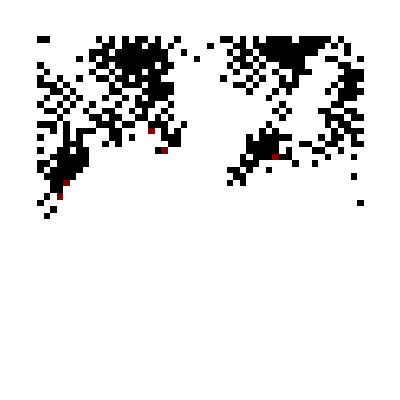

```mathematica
ArrayPlot[%]
```